```mathematica
eqsB={B1'[t]==r1 B1[t]-I B3[t](Conjugate[B1[t]]+(1/(1-b)-b St^2+I (b St)/(1-b))Conjugate[B3[t]]),B3'[t]==r3 B3[t]+I B3[t](-δ+Conjugate[B1[t]]+(1/(1-b)-b St^2+I (b St)/(1-b))Conjugate[B3[t]])}
```

{B1'[t]==r1 B1[t]-ⅈ B3[t] (Conjugate[B1[t]]+(99.9901+9.9 ⅈ) Conjugate[B3[t]]),B3'[t]==r3 B3[t]+ⅈ B3[t] (-δ+Conjugate[B1[t]]+(99.9901+9.9 ⅈ) Conjugate[B3[t]])}

```mathematica
eqsBman={B3'[t]==r3 B3[t]+I B3[t](-δ+(-I B3[t]((1/(1-b)-b St^2-I (b St)/(1-b))Conjugate[B3[t]]))/r1+(1/(1-b)-b St^2+I (b St)/(1-b))Conjugate[B3[t]])}
```

{B3'[t]==r3 B3[t]+ⅈ B3[t] (-δ+(99.9901+9.9 ⅈ) Conjugate[B3[t]]-((9.9+99.9901 ⅈ) B3[t] Conjugate[B3[t]])/r1)}

```mathematica
replH={r1->0,r3->0,δ->0}
```

{r1→0,r3→0,δ→0}

```mathematica
replFull={r1->-1/St,r3->-(1-b)St,δ->1}
```

{r1→-10.,r3→-0.001,δ→1}

Case 1: parameters are such that the variable B1 quickly decays to zero, leaving us with a reduced system for the variable B3 that can be further simplified: a constant of motion can be found.

```mathematica
St=0.1;b=0.99;ϵ=0.3;
Mtemp=-St^2/ϵ+1/(ϵ(1-b))-I St/(ϵ(1-b));σ0=1.;ω0=1/Mtemp;solB=NDSolve[Join[eqsB/.replFull,{B1[0]==ω0-Conjugate[σ0]/(-St^2/ϵ+1/(ϵ(1-b))-I St/(ϵ(1-b))),B3[0]==Conjugate[σ0]/(-St^2/ϵ+1/(ϵ(1-b))-I St/(ϵ(1-b)))}],{B1[t],B3[t]},{t,0,10000}];solBman=NDSolve[Join[eqsBman/.replFull,{B3[0]==Conjugate[σ0]/(-St^2/ϵ+1/(ϵ(1-b))-I St/(ϵ(1-b)))}],{B3[t]},{t,0,10000}]
```

{{B3[t]→InterpolatingFunction[{{0., 10000.}}, <>][t]}}

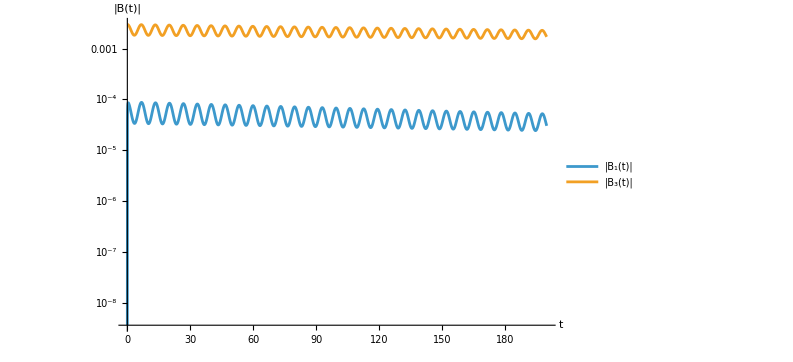

```mathematica
LogPlot[Evaluate[{Abs[B1[t]],Abs[B3[t]]}/.replFull/.solB[[1]]],{t,0,200},PlotRange->All,PlotLegends->{"|B₁(t)|", "|B₃(t)|"}, AxesLabel->{"t", "|B(t)|"}]
```

```mathematica
{r1,r3}/.replFull
```

{-10.,-0.001}

```mathematica
-I B3[t](Conjugate[B1[t]]+(1/(1-b)-b St^2+I (b St)/(1-b))Conjugate[B3[t]])
```

-ⅈ B3[t] (Conjugate[B1[t]]+(99.9901+9.9 ⅈ) Conjugate[B3[t]])

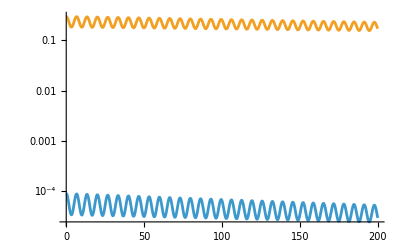

```mathematica
LogPlot[Evaluate[{Abs[(-I B3[t]((1/(1-b)-b St^2-I (b St)/(1-b))Conjugate[B3[t]]))/r1],Abs[+(1/(1-b)-b St^2+I (b St)/(1-b))Conjugate[B3[t]]]}/.replFull/.solB[[1]]],{t,0,200},PlotRange->All]
```

```mathematica
(1/(1-b)-b St^2-I (b St)/(1-b))
```

99.9901-9.9 ⅈ

```mathematica
1/(1-b)*1/b
```

101.01

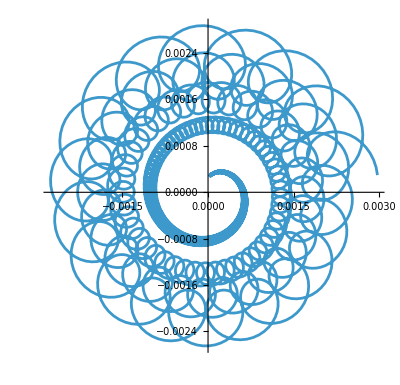

```mathematica
ParametricPlot[{Re[B3[t]Exp[I t]],Im[B3[t]Exp[I t]]}/.solB[[1]],{t,0,2000},PlotRange->All,PlotPoints->200]
```

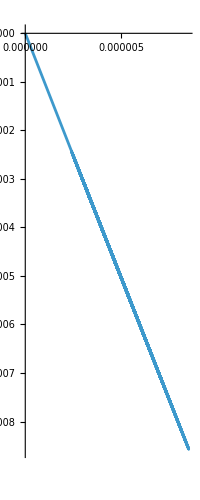

```mathematica
ParametricPlot[{Re[B1[t]],Im[B1[t]]}/.solB[[1]],{t,0,200},PlotRange->All]
```

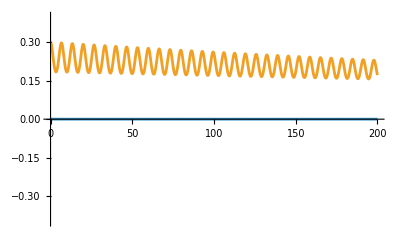

```mathematica
Plot[Evaluate[{Abs[B1[t]],Abs[(1/(1-b)-b St^2+I (b St)/(1-b))Conjugate[B3[t]]]}/.solB[[1]]],{t,0,200},PlotRange->0.4*{-1,1}]
```

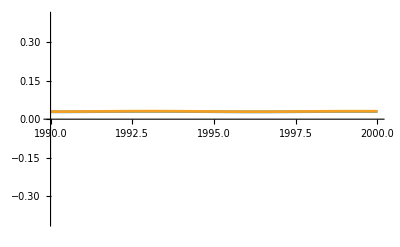

```mathematica
Plot[Evaluate[{Abs[(1/(1-b)-b St^2+I (b St)/(1-b))Conjugate[B3[t]]]/.solB[[1]],Abs[(1/(1-b)-b St^2+I (b St)/(1-b))Conjugate[B3[t]]]/.solBman[[1]]}],{t,1990,2000},PlotRange->0.4*{-1,1}]
```

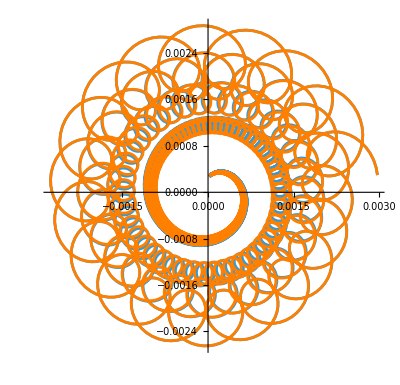
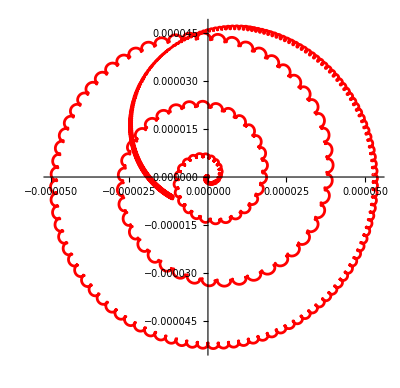
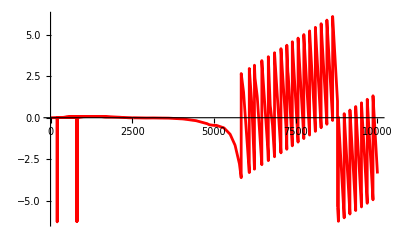

```mathematica
flowerB=ParametricPlot[{Re[B3[t]Exp[I t]],Im[B3[t]Exp[I t]]}/.solB[[1]],{t,0,2000},PlotRange->All,PlotPoints->200];flowerBman=ParametricPlot[{Re[B3[t]Exp[I t]],Im[B3[t]Exp[I t]]}/.solBman[[1]],{t,0,2000},PlotRange->All,PlotPoints->200,PlotStyle->Orange];flowerDiff=ParametricPlot[({Re[B3[t]Exp[I t]],Im[B3[t]Exp[I t]]}/.solB[[1]])-({Re[B3[t]Exp[I t]],Im[B3[t]Exp[I t]]}/.solBman[[1]]),{t,0,2000},PlotRange->All,PlotPoints->500,PlotStyle->Red];
argDiff=Plot[Arg[(B3[t]Exp[I t]/.solB[[1]])]-Arg[(B3[t]Exp[I t]/.solBman[[1]])],{t,0,10000},PlotRange->All,PlotPoints->500,PlotStyle->Red];{Show[flowerB,flowerBman],Show[flowerDiff],Show[argDiff]}
```

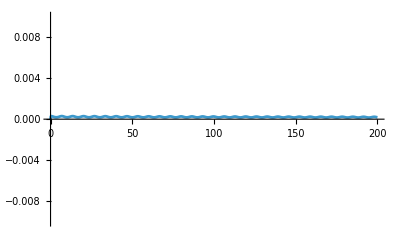

```mathematica
Plot[Evaluate[Abs[B1[t]]/Abs[(1/(1-b)-b St^2+I (b St)/(1-b))Conjugate[B3[t]]]/.solB[[1]]],{t,0,200},PlotRange->{-.01,.01}]
```

```mathematica
Plot[Evaluate[Abs[B1[t]]/Abs[(1/(1-b)-b St^2+I (b St)/(1-b))Conjugate[B3[t]]]/.solB[[1]]],{t,0,200},PlotRange->{-.01,.01}]
```

-Graphics-

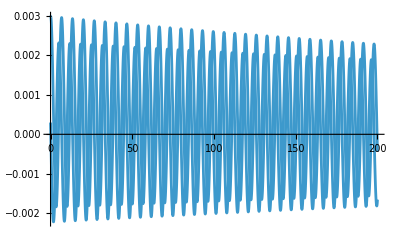

```mathematica
Plot[{Re[B3[t]],Im[B3[t]]}/.solB[[1]],{t,0,200},PlotRange->All]
```

```mathematica
{1/(B3[t]B4[t])B3'[t]==((-1+b) St)/B4[t]+I (-1/B4[t]+(1/(1-b)-b St^2+I (b St)/(1-b))),1/(B3[t]B4[t])B4'[t]==((-1+b) St)/B3[t]-I (-1/B3[t]+(1/(1-b)-b St^2-I (b St)/(1-b)))}
```

{B3'[t]/(B3[t] B4[t])==ⅈ ((99.9901+9.9 ⅈ)-1/B4[t])-0.001/B4[t],B4'[t]/(B3[t] B4[t])==-ⅈ ((99.9901-9.9 ⅈ)-1/B3[t])-0.001/B3[t]}

```mathematica
Happrox[t_]:=(B3[t] (-1-b^2 St^2+b St (ⅈ+St)))/(-1+b)+ⅈ (ⅈ+(-1+b) St) Log[B3[t]]-1/(-1+b)(Conjugate[B3[t]] (1+b^2 St^2-b St (-ⅈ+St))+(-1+b) (1+ⅈ (-1+b) St) Log[Conjugate[B3[t]]])
```